```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/c/Repositories/BBN/pyBBN/src/tests/photon_electron_neutrino_universe

### Parcing log.txt file

```mathematica
readLines[lines_]:=Map[(
s=StringToStream[#];
x =Read[s,Number];
Close[s];
x
)&,StringSplit/@lines,{2}];
lines = Import["output/evolution.txt", {"Text", "Lines"}][[2;; ]] // readLines;
```

```mathematica
cols= Transpose@lines;
```

```mathematica
(*# aT,MeV T,MeV a x,MeV t,s rho,MeV^4 N_eff fraction S,MeV^3*)
tdat=lines[[All,5]];
Tdat=lines[[All,2]];
ρdat=lines[[All,6]];
adat=lines[[All,3]];
aTdat=lines[[All,1]];
Neffdat=lines[[All,7]];
```

### Genelar constants

```mathematica
gg =2+7/8*(4+6);
Mpl=1.220910 * 10^22/(1.66 √gg) (*MeV*);
```

```mathematica
G=(10^-22/1.220910)^2;
```

```mathematica
T0=100(*MeV*);
```

```mathematica
MevToSec=6.5821220 10^-22;
```

```mathematica
me=0.511(*MeV*);
```

```mathematica
ge=4;
gν=6;
gγ=2;
```

### Some basic definitions

```mathematica
fFermi[p_,T_,m_]:=1/(ⅇ^((√(p^2+m^2))/T)+1)
```

```mathematica
ρFermi[T_,m_]:=gf NIntegrate[(4 π)/(2π)^3 fFermi[p,T,m] p^2 √(p^2+m^2),{p,0,∞}]
```

## Energy density from scale factor

### Some calculation

ρ=const* a^-4=ρ0 a0^4* a^-4
a0=1/T0
ρ0=π^2/30 g* T0^4*10^24
const=ρ0 a0^4=π^2/30 g*
factor 10^24 appears due to MeV^4→ eV^4 convertation

```mathematica
constρ=π^2/30 gg*10^24//N
```

3.53661×10^24

```mathematica
ρadat=Transpose[{adat,ρdat}];
```

```mathematica
ρtdat=Transpose[{tdat,ρdat}];
```

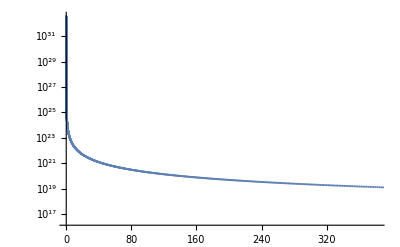

```mathematica
ListLogPlot[ρtdat]
```

```mathematica
ρafitcurve=Fit[ρadat[[2305 ;; ]],{a^-4},a]
```

(4.16795×10^24)/a^4

```mathematica
Show[Plot[constρ a^-4,{a,0,10},PlotStyle-> {Green,Thick}],Plot[ρafitcurve,{a,0,10},PlotStyle->{Red,Dashed}],ListPlot[ρadat[[;; ;; 15]]],PlotLabel->Style[#,Bold,15]&/@{"ρ(a)"},Frame-> True, FrameLabel->{"a [1]","ρ [eV^4]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Fitting:" @ρafitcurve}],LineLegend[{Green},{" Analytically:" @constρ a^-4}]}]],Bold,10],Scaled[{0.98,0.98}],Scaled[{1,1}]], ImageSize-> Large]
```

-Graphics-

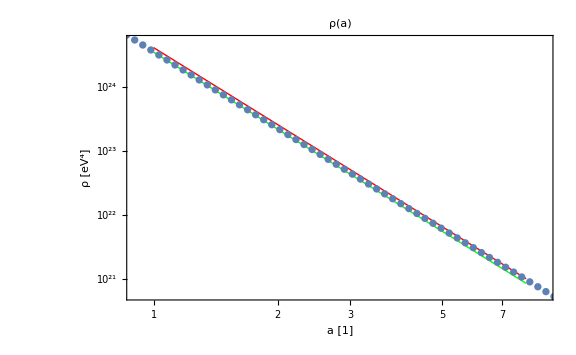

```mathematica
Show[LogLogPlot[constρ a^-4,{a,1,8},PlotStyle-> {Green,Thick}],LogLogPlot[ρafitcurve,{a,1,8},PlotStyle->{Red,Thick}],ListLogLogPlot[ρadat[[;; ;; 15]],PlotRange->{{1,8},Automatic}],PlotLabel->Style[#,Bold,15]&/@{"ρ(a)"},Frame-> True, FrameLabel->{"a [1]","ρ [eV^4]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Fitting:" @ρafitcurve}],LineLegend[{Green},{" Analytically:" @(constρ a^-4)}]}]],Bold,10],Scaled[{0.98,0.98}],Scaled[{1,1}]], ImageSize-> Large]
```

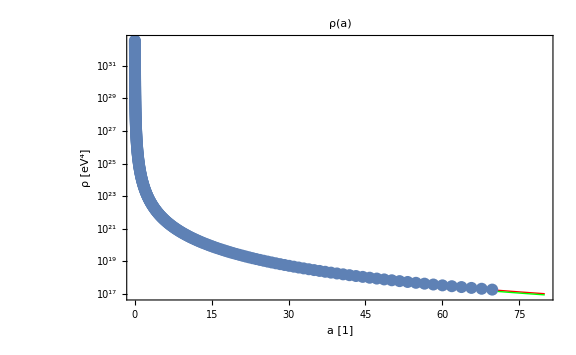

```mathematica
Show[LogPlot[ρafitcurve,{a,0.001,80},PlotStyle->{Red,Thick}],LogPlot[constρ a^-4,{a,0.001,80},PlotStyle->{Green,Thick}],
ListLogPlot[ρadat[[;;;;10]],PlotStyle->{PointSize[.015]}],
PlotLabel->Style[#,Bold,15]&/@{"ρ(a)"},FrameLabel->{"a [1]","ρ [eV^4]"},PlotRange->All,AxesOrigin->{0,0}, Axes->False,Frame->True,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Green},{" Analytically:" @constρ a^-4}],LineLegend[{Red},{" Fitting:" @ρafitcurve}]}]],Bold,12],Scaled[{0.98,0.98}],Scaled[{1,1}]],ImageSize->Large]
```

## Energy density from temperature

### Massive electrons

```mathematica
ρTdat=Transpose[{Tdat,ρdat}];
```

```mathematica
ListPlot[ρTdat]
```

-Graphics-

```mathematica
ρMassiveEl=ρFermi[#,me]/. gf-> ge&/@Tdat;
ρMasslessEl=7/8 ge π^2/30(#)^4&/@Tdat;
```

```mathematica
ργ=gγ π^2/30(#)^4&/@Tdat;
```

Taking into account that for neutrinos it s always true that aν*Tν=1:

```mathematica
ρν=7/8 gν π^2/30(#)^4&/@((adat)^-1);
```

```mathematica
ρTγe=Transpose[{Tdat,(ργ+ρν+ρMassiveEl)*10^24}];
```

```mathematica
Show[ListPlot[ρTγe,PlotStyle-> {Green,Thick}],ListPlot[ρTdat[[;; ;; 15]],PlotRange->{{3,20},Automatic}],PlotLabel->Style[#,Bold,15]&/@{"ρ(T)"},Frame-> True, FrameLabel->{"T [MeV]","ρ [eV^4]"},Axes->  None,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],PointLegend[{Green},{" Calculated for massive e" }]}]],Bold,10],Scaled[{0.42,0.98}],Scaled[{1,1}]], ImageSize-> Large,PlotRange->All]
```

-Graphics-

## Scale factor from time

### Some calculations

a = const* √t=a0 √(t/t0)
t0=1/(2H0)=Mpl^*/(2 T0^2)

Convert Mev^-1 to sec:

```mathematica
t0=Mpl/(2 T0^2)MevToSec
```

0.0000738256

```mathematica
a0 = 1/T0
```

1/100

```mathematica
const=a0/(√t0)
```

1.16385

### Plots

```mathematica
atdat = Transpose[{tdat, adat}];
```

```mathematica
atfitcurve=Fit[atdat,{t^(1/2)},t]
```

1.21827 √t

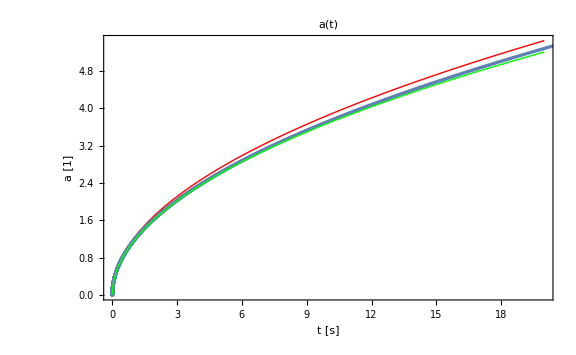

```mathematica
Show[Plot[atfitcurve,{t,0,20},PlotStyle->{Red,Thick}],ListPlot[atdat,PlotRange->{{0,20},{0,0.002}}],Plot[const  √t,{t,0,20},PlotStyle->{Green,Thick}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Fitting:" @atfitcurve}],LineLegend[{Green},{" Analytically:" @const √t}]}]],Bold,10],Scaled[{0.98,0.45}],Scaled[{1,1}]],ImageSize->Large]
```

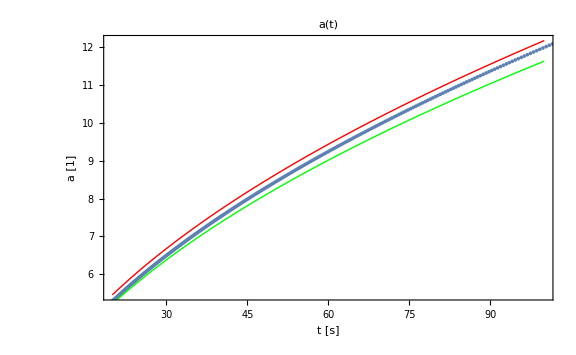

```mathematica
Show[Plot[atfitcurve,{t,20,100},PlotStyle->{Red,Thick}],ListPlot[atdat],Plot[const  √t,{t,20,100},PlotStyle->{Green,Thick}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Fitting:" @atfitcurve}],LineLegend[{Green},{" Analytically:" @const √t}]}]],Bold,10],Scaled[{0.98,0.45}],Scaled[{1,1}]],ImageSize->Large]
```

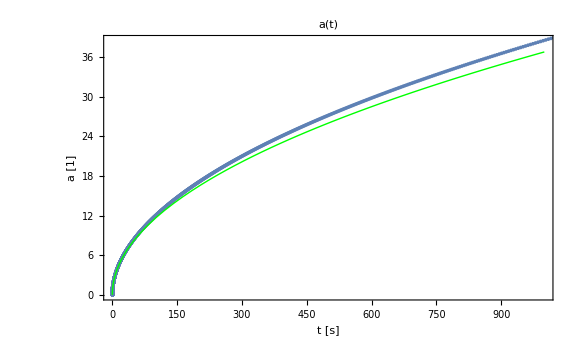

```mathematica
Show[Plot[atfitcurve,{t,0,1000},PlotStyle->{Red,Thick}],ListPlot[atdat],Plot[const  √t,{t,0,1000},PlotStyle->{Green,Thick}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Fitting:" @atfitcurve}],LineLegend[{Green},{" Analytically:" @const √t}]}]],Bold,10],Scaled[{0.98,0.45}],Scaled[{1,1}]],ImageSize-> Large]
```

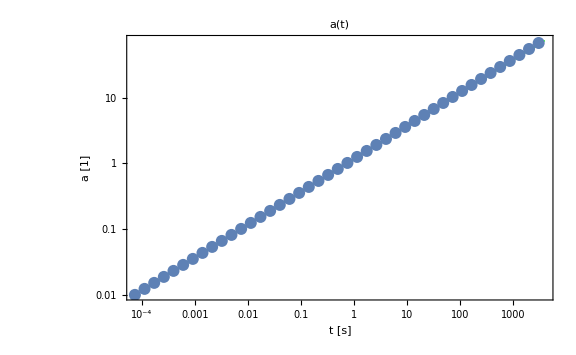

```mathematica
Show[LogLogPlot[const √t,{t,0.0001,4000},PlotStyle->{Green,Thick}],ListLogLogPlot[atdat[[;;;;70]],PlotStyle->{PointSize[.015]}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},FrameLabel->{"t [s]","a [1]"},PlotRange->All,AxesOrigin->{0,0}, Axes->False,Frame->True,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Green},{" Analytically:" @const √t}]}]],Bold,12],Scaled[{0.98,0.35}],Scaled[{1,1}]],ImageSize->Large]
```

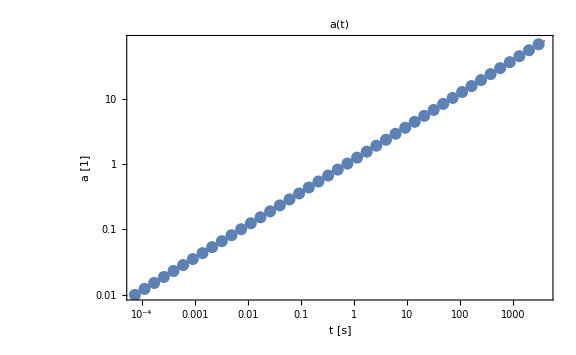

```mathematica
Show[LogLogPlot[atfitcurve, {t, 0.0001, 4000}, PlotStyle -> {Red, Thick}], ListLogLogPlot[atdat[[;; ;; 70]], PlotStyle -> {PointSize[.015]}], PlotLabel -> Style[#, Bold, 15] & /@ {"a(t)"}, FrameLabel -> {"t [s]", "a [1]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, Epilog -> Inset[Style[Framed[Column[{PointLegend[{Blue}, {" Data"}], LineLegend[{Red}, {" Fitting:" @atfitcurve}]}]], Bold, 12], Scaled[{0.98, 0.35}], Scaled[{1, 1}]], ImageSize -> Large]
```

### Massive electrons

```mathematica
ρtota=Transpose[{adat,(ργ+ρν+ρMassiveEl)}];
ρtotaMassless=Transpose[{adat,(ργ+ρMasslessEl)}];
```

```mathematica
ρtotaFunc=Interpolation[ρtota];
ρtotaMasslessFunc=Interpolation[ρtotaMassless];
```

```mathematica
aTime=Parallelize[NDSolve[{((D[a[t],t]MevToSec)/a[t])^2==(8π)/3 G ρtotaFunc[a[t]],a[t0]==0.01},a,{t,t0,1000}]]
aTimeMassless=NDSolve[{((D[a[t],t]MevToSec)/a[t])^2==(8π)/3 G ρtotaMasslessFunc[a[t]],a[t0]==0.01},a,{t,t0,1000}]
```

{{a→InterpolatingFunction[{{0.0000738256, 1000.}}, <>]},{a→InterpolatingFunction[{{0.0000738256, 1000.}}, <>]}}

{{a→InterpolatingFunction[{{0.0000738256, 0.000282042}}, <>]},{a→InterpolatingFunction[{{0.0000738256, 1000.}}, <>]}}

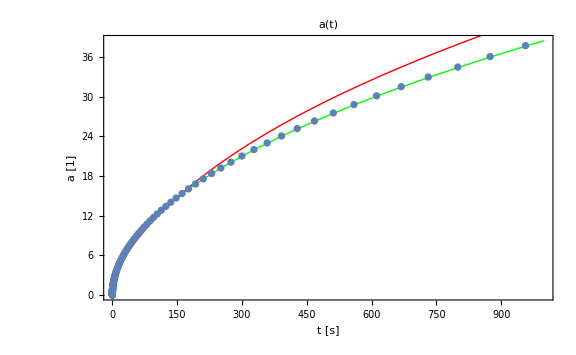

```mathematica
Show[Plot[Evaluate[a[t]/.aTime[[2]]],{t,t0,1000},PlotStyle->{Green,Thick}],Plot[Evaluate[a[t]/.aTimeMassless[[2]]],{t,t0,1000},PlotStyle->{Red,Thick}],ListPlot[atdat[[;; ;; 15]],PlotRange->{{t0,100},Automatic}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Axes->  None,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],PointLegend[{Red},{" Calculated for massless e" }],PointLegend[{Green},{" Calculated for massive e" }]}]],Bold,10],Scaled[{0.98,0.38}],Scaled[{1,1}]], ImageSize-> Large]
```

## Scale factor from temperature

```mathematica
ρTdat=Transpose[{Tdat,adat}];
```

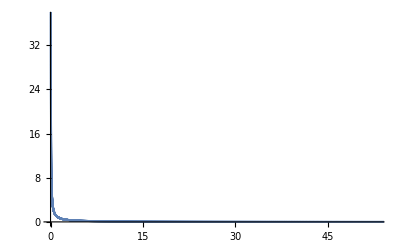

```mathematica
ListPlot[ρTdat]
```

## a*T

```mathematica
adat*Tdat;
```

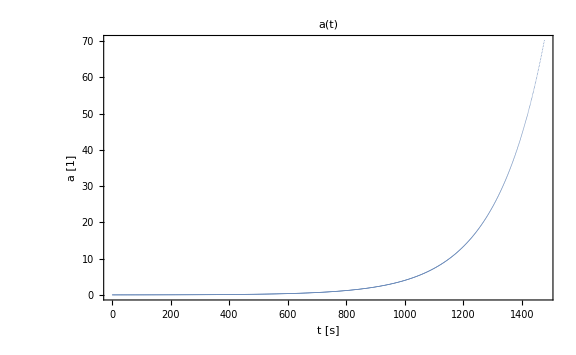

```mathematica
Show[ListPlot[adat[[;; ;; 2]], PlotStyle -> {PointSize[.001]}], PlotLabel -> Style[#, Bold, 15] & /@ {"a(t)"}, FrameLabel -> {"t [s]", "a [1]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

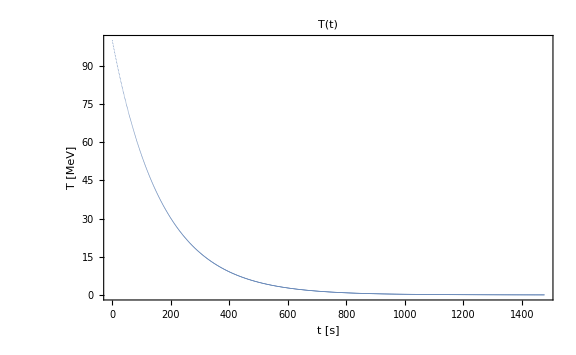

```mathematica
Show[ListPlot[Tdat[[;; ;; 2]], PlotStyle -> {PointSize[.001]}], PlotLabel -> Style[#, Bold, 15] & /@ {"T(t)"}, FrameLabel -> {"t [s]", "T [MeV]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

```mathematica
aTt = Transpose[{tdat, aTdat}];
```

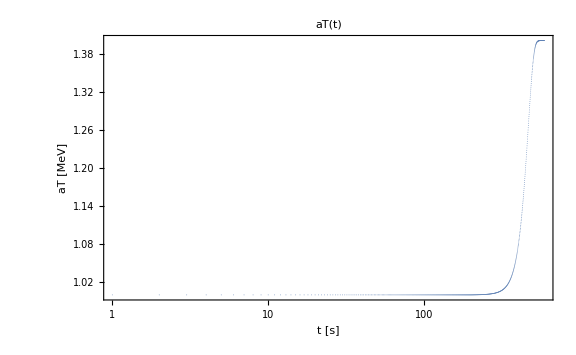

```mathematica
Show[ListLogLinearPlot[aTdat[[;; ;; 5]], PlotStyle -> {PointSize[.001]}], PlotLabel -> Style[#, Bold, 15] & /@ {"aT(t)"}, FrameLabel -> {"t [s]", "aT [MeV]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

aT is not conserving, starting from the temperature [MeV] (t=15 s):

```mathematica
TaT=√(Mpl/(2 15)MevToSec)
```

0.221849

## Neff from time

ρ=ρ(photons)+ρ(relativistic fermions)
Neff - number of relativistic fermions
Neff=(ρ-π^2/15 T^4)/(7/8 π^2/15 (T/1.4)^4) (

```mathematica
Nefftdat=Transpose[{tdat,Neffdat}];
```

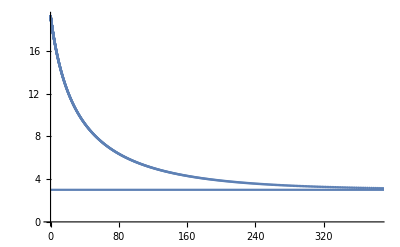

```mathematica
Show[ListPlot[Nefftdat],Plot[3,{t,0,3000}]]
```

## Comparison with articles

#### Ruchayskiy, Ivashko https://arxiv.org/pdf/1202.2841.pdf, figure 9

```mathematica
Fig9=Transpose[{1/Tdat,aTdat}];
```

```mathematica
Fig92=Transpose[{adat,aTdat}];
```

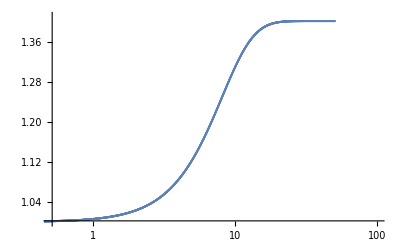

```mathematica
ListLogLinearPlot[Fig9,PlotRange->{{0.5,100},{1,1.41}}]
```

```mathematica
PhElνTestFunc=Interpolation[Fig9];
PhElνTestFunc2=Interpolation[Fig92];
```

```mathematica
smTxTest=Import["../../figures/Figures-sources/sm-Tx_comp/semi_sm_upd_x.dat","HeaderLines"->2];
smTxTestFunc=Interpolation[smTxTest[[All,{1,3}]]];
smTxDigit=Import["../../figures/Figures-sources/sm-Tx_comp/sm_temp.dat","HeaderLines"->1];
smTxDigitFunc=Interpolation[smTxDigit[[All,{1,2}]]];
```

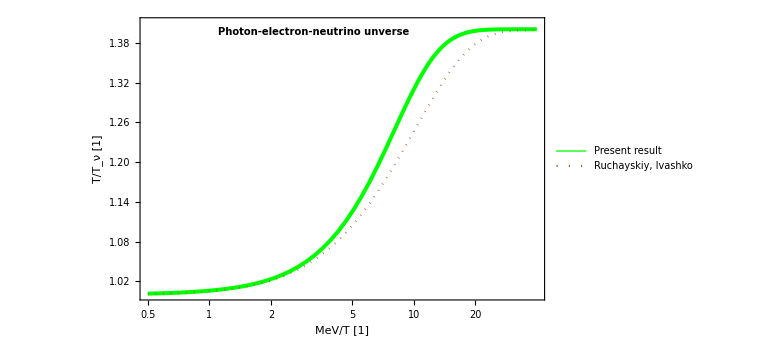

```mathematica
LogLinearPlot[{PhElνTestFunc[x],smTxTestFunc[x]},{x,0.5,40},PlotRange->{{0.5,40},{1,1.41}},Frame->True,FrameLabel->{"MeV/T [1]","T/T_ν [1]"},PlotLegends->{"Present result","Ruchayskiy, Ivashko"},PlotStyle->{{Thickness[0.005],Green},{Dotted,Brown},{Dashed,Gray}},Epilog->Inset[Style[Framed[Text["Photon-electron-neutrino unverse"]],Bold,10],Scaled[{0.43,0.95}],Scaled[{1,1}]],ImageSize->Large]
(*Export["/home/stasya/Desktop/Link to 2master/1BBN/test_results/photon-electron-neutrino_universe/RA.png",%];*)
```

InterpolatingFunction::dmval: Input value {0.500045} lies outside the range of data in the interpolating function. Extrapolation will be used.

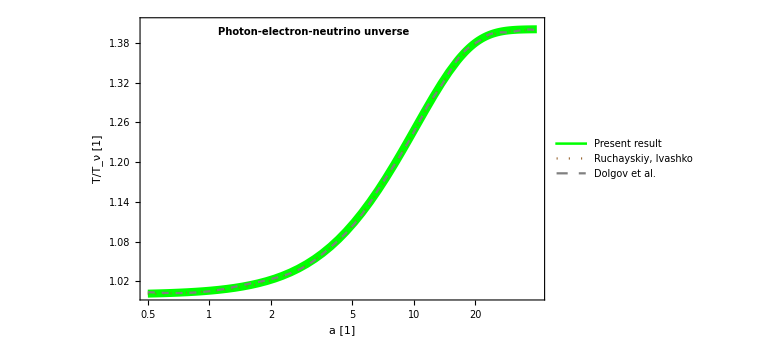

```mathematica
LogLinearPlot[{PhElνTestFunc2[x],smTxTestFunc[x],smTxDigitFunc[x]},{x,0.5,40},PlotRange->{{0.5,40},{1,1.41}},Frame->True,FrameLabel->{"a [1]","T/T_ν [1]"},PlotLegends->{"Present result","Ruchayskiy, Ivashko","Dolgov et al."},PlotStyle->{{Thickness[0.01],Green},{Dotted,Brown},{Dashed,Gray}},Epilog->Inset[Style[Framed[Text["Photon-electron-neutrino unverse"]],Bold,10],Scaled[{0.43,0.95}],Scaled[{1,1}]],ImageSize->Large]
(*Export["/home/stasya/Desktop/Link to 2master/1BBN/test_results/photon-electron-neutrino_universe/RAD.png",%];*)
```